# OS3180 Final Exam

## Steve Mazza

## Problem 1

Interpretation of this problem has me treating the first and second halves of the problem independently and then multiplying their results.  The first half is easy... we calculate the probability that the signal will not get through either the top or bottom branch as follows (they are the same probability):

```mathematica
1-0.9
```

0.1

Then calculate the combined probability the signal will pass throught the first (left) half of the network:

```mathematica
1-(0.1*0.1)
```

0.99

Next calculate the probability the signal will not pass through the top branch of the second (right) half of the network:

```mathematica
1-(0.95*0.95)
```

0.0975

And the probability that the signal will not pass thought the bottom half of the second (right) half of the network:

```mathematica
1-0.85
```

0.15

Now the combined probability that the signal will pass through the second (right) half of the network:

```mathematica
1-(0.0975*0.15)
```

0.985375

Last, calculate the probability that the signal will pass through the entire network:

```mathematica
0.99*0.985375
```

0.975521

## Problem 2

### Part a)

NOTE: The assumption for this problem is that there exist only two (2) types of armor: rolled homogeneous and composite.
Begin by interpreting the results of the penetration test:

```mathematica
40/50.0
```

0.8

```mathematica
25/50.0
```

0.5

P(penetrate rolled homogeneous armor) = 0.8
P(penetrate composite armor) = 0.5
P(enemy uses rolled homogeneous armor) = 0.8
P(enemy uses composite armor) = 0.2

Next calculate P(armor penetration) = (P(penetration | composite armor) × P(composite armor)) × (P(penetration | rolled armor) × P(rolled armor)):

```mathematica
(0.8*0.8)+(0.5*0.2)
```

0.74

### Part b)

Calculate P(composite armor | failed penetration)
= P(failed penetration ∩ composite armor) ÷ P(failed penetration)
= P(failed penetration | composite armor) × P(composite armor) ÷ P(failed penetration)

```mathematica
(0.5*0.2)/(1-0.74)
```

0.384615

## Problem 3

GIVEN: No false positives!

### Part a)

Calculate P(detection | presence) × P(presence)

```mathematica
0.24*0.05
```

0.012

### Part b)

Calculate P(no presence | no detection) 
= P(no detection ∩ presence) ÷ P(presence)
= P(no detection | presence) × P(presence) ÷ P(no detection)

```mathematica
(0.76*0.05)/(1-0.012)
```

0.0384615

### Part c)

First calculate the probabiility that one search would not detect the Scorpion:

```mathematica
1-0.24
```

0.76

Now calculate the odds for two:

```mathematica
0.76^2
```

0.5776

## Problem 4

### Part a)

This is the Binomial Distribution: P(X⩾6).

### Part b)

Calculate E(X) based on the 80% chance of completing the mission (rounded down since you can’t have partial helicopters in the air):

```mathematica
Floor[8*0.8]
```

6

### Part c)

Calculate the sum of probabilities 0...5 to determine the probability of mission failure:

```mathematica
(Binomial[8,0]*0.8^0*0.2^8)+(Binomial[8,1]*0.8^1*0.2^7)+(Binomial[8,2]*0.8^2*0.2^6)+(Binomial[8,3]*0.8^3*0.2^5)+(Binomial[8,4]*0.8^4*0.2^4)+(Binomial[8,5]*0.8^5*0.2^3)
```

0.203082

### Part d)

The conclusions are predicated on the assumption that helicopter failure is an independent random variable.  If failure of one helicopter affects the probability of failure of another, then these are invalid conclusions.  I do not believe this is the case, however.  And so I believe that the assumption of independence has been met.

## Problem 5

### Part a)

First calculate the standard deviation for 6 pallettes:

```mathematica
√(6.0*200^2)
```

489.898

Next calculate the mean for the 6 pallettes:

```mathematica
6*1323
```

7938

Next calculate the standard deviation for 90 troops:

```mathematica
√(90.0*20^2)
```

189.737

Next calculate the mean for the 90 troops:

```mathematica
90*180
```

16200

Use the rules for sums of random variables to combine the totals for the mean:

```mathematica
16200+7938
```

24138

Use the rules for sums of random variables to combine the totals for the standard deviation:
NOTE: These are independent random variables and so Cov(X_1, X_2)=0.

```mathematica
√(189.737^2+489.898^2+0)
```

525.357

### Part b)

X=N(24138,525.357^2)
P(X>25000)=1-Φ(-862/525.357)
=1-Φ(-1.640789)
=1-0.0505

```mathematica
1 - 0.0505
```

0.9495

## Problem 6

NOTE: I am assuming that I can add simply take the 45 seconds off the top of the calculation by increasing the response time.
Calculate: P(N(4,0.25^2) > N(2.75, 0.5^2)+0.75)
=P(N(4-2.75, 0.25^2+0.5^2)>0)
=P(N(0,1)>-1.25/(√0.3125))
=1-Φ(-2.23607)
=1-0.0126736

```mathematica
1-0.012673593107712471
```

0.987326

## Problem 7

### Part a)

Observed value = 0.06.
We use this value to calculate the Standard Error:

```mathematica
(√(0.06*(1-0.06)))/(√600)
```

0.00969536

Now we use the computed standard error and the value 1.96 from the table to compute our interval:

```mathematica
1.96*0.009695359714832659
```

0.0190029

Our 95% confidence interfal is 0.06 ± 0.0190029 or, 0.0409971 ⩽ p ⩽ 0.0790029

### Part b)

NOTE: Anser is rounnded up since you can’t survey a partial person.

```mathematica
Ceiling[(1.64^2*0.06*(1-0.06))/0.01^2]
```

1517

## Problem 8

### Part a)

Calculate Z_O:

```mathematica
(0.208-0.15)/((√(0.15*(1-0.15)))/(√125))
```

1.81605

Compute the p-value:

```mathematica
<<Statistics`HypothesisTests`
```

```mathematica
NormalPValue[1.8160504441469336]
```

OneSidedPValue→0.0346813

H_0: The observations are the result of chance.
H_A: The system performance is different than expected.
Conclusion: Since the p-value is less than α, we must rule out H_0 and determine that the observations are different than expected.

### Part b)

The p-value tells us how likely we are to obtain our observed results if H_0is true.

## Problem 9

### Part a)

```mathematica
m=({{21.0, 61}, {28.3, 87}, {27.5, 98}, {26.8, 104}, {28.3, 102}, {30.5, 63}, {30.8, 27}, {33.6, 14}, {31.3, 30}, {33.0, 67}, {34.3, 6}, {33.0, 18}, {32.0, 42}, {27.8, 60}, {25.0, 82}, {26.0, 77}, {18.0, 108}, {24.8, 77}, {26.0, 93}, {27.1, 100}, {29.0, 118}, {34.0, 74}, {28.3, 43}, {31.0, 19}, {31.8, 23}, {33.5, 25}, {34.5, 40}, {34.3, 21}, {26.5, 23}, {27.3, 56}, {25.8, 59}, {18.5, 89}, {19.0, 102}, {16.3, 97}})
```

{{21.,61},{28.3,87},{27.5,98},{26.8,104},{28.3,102},{30.5,63},{30.8,27},{33.6,14},{31.3,30},{33.,67},{34.3,6},{33.,18},{32.,42},{27.8,60},{25.,82},{26.,77},{18.,108},{24.8,77},{26.,93},{27.1,100},{29.,118},{34.,74},{28.3,43},{31.,19},{31.8,23},{33.5,25},{34.5,40},{34.3,21},{26.5,23},{27.3,56},{25.8,59},{18.5,89},{19.,102},{16.3,97}}

```mathematica
model=LinearModelFit[m,x, x]
```

FittedModel[182.139-4.28077 x]

```mathematica
reg=Regress[m,{1,x},x]
```

{ParameterTable→ | Estimate | SE | TStat | PValue
1 | 182.139 | 25.4785 | 7.14872 | 4.09554×10^-8
x | -4.28077 | 0.893476 | -4.79115 | 0.00003643,RSquared→0.417706,AdjustedRSquared→0.39951,EstimatedVariance→661.936,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 15194.8 | 15194.8 | 22.9551 | 0.00003643
Error | 32 | 21181.9 | 661.936 |  | 
Total | 33 | 36376.7 |  |  | }

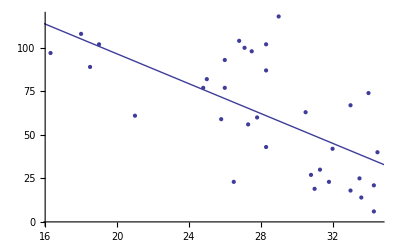

```mathematica
Show[ListPlot[m],Plot[model["BestFit"],{x,0,130}]]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 182.139 | 25.4785 | 7.14872 | 4.09554×10^-8
x | -4.28077 | 0.893476 | -4.79115 | 0.00003643

The error seems high so I would say that the utility of this model is fairly low.

### Part b)

Calculate the estimate for successful detections at 25° C:

```mathematica
model[25]
```

75.1192

Re-calculate the estimate at 25° C and provide a 95% confidence interval for the estimate:

```mathematica
fit      lwr     upr
75.11921 64.52173 85.7167
```

### Part c)

Re-calculate the estimate at 25° C and provide a 95% prediction interval for the estimate:

```mathematica
fit      lwr      upr
75.11921 21.65201 128.5864
```

## Problem 10

### Part a)

r = 0.6900

### Part b)

Calculate R^2by first calculating the missing value for Sum of Squares on the ANOVA table:

```mathematica
(308.6447-161.7146)/308.6447
```

0.476049

### Part c)

Calculate standard error by first calculating MSE:

```mathematica
√(161.7146/(19+1-2))
```

2.99736

### Part d)

n = 20